```mathematica
SetDirectory["/Users/Mukesh/Documents/Research/RSD"]
```

/Users/Mukesh/Documents/Research/RSD

```mathematica
da=ReadList["hydra_matterpower_z0.dat",{Number,Number}];
kCAMB=Flatten[Drop[da,{},{2,2}]];
PkCAMB=Flatten[Drop[da,{},{1,1}]];
PlinHydra=Interpolation[da];
```

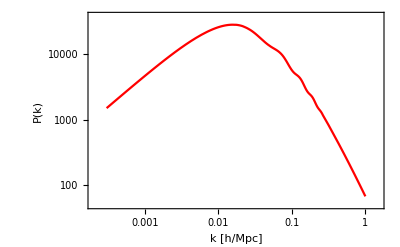

```mathematica
LogLogPlot[PlinHydra[k],{k,0.0003,1},Frame->True,PlotStyle->Red,LabelStyle->{Italic,FontFamily->"Helvetica"},FrameLabel->{"k [h/Mpc]","P(k)"},ColorFunctionScaling->False,ImageSize->400,FrameTicksStyle->20,FrameStyle->21]
```

```mathematica
xs = ReadList["xs.dat", {Number,Number,Number}]
```

{{1,41,46},{1,41,47},{1,41,48},{1,41,49},{1,41,50},{1,41,51},{1,41,52},{1,41,53},{1,41,54},{1,42,45},{1,42,46},{1,42,47},{1,42,48},{1,42,49},{1,42,50},{1,42,51},{1,42,52},{1,42,53},{1,42,54},{1,42,55},{1,43,43},{1,43,44},523112,{99,57,57},{99,58,45},{99,58,46},{99,58,47},{99,58,48},{99,58,49},{99,58,50},{99,58,51},{99,58,52},{99,58,53},{99,58,54},{99,58,55},{99,59,46},{99,59,47},{99,59,48},{99,59,49},{99,59,50},{99,59,51},{99,59,52},{99,59,53},{99,59,54}}
 |  |  |  |

```mathematica
L=100;
Ng = 0;
Do[Do[Do[If[(i-L/2)^2+(j-L/2)^2+(k-L/2)^2<(L/2)^2,Ng++],{k,L}],{j,L}],{i,L}];
```

523155

```mathematica
d = {0,0,100}
```

{0,0,100}

```mathematica
J[k1_,k2_] := 1/Ng^3*Sum[(k1.(d+xs[[i]]))*(k2.(d+xs[[i]]))*Exp[-ⅈ*((k1+k2).xs[[i]])],{i,Ng}]
```

```mathematica
N[J[{0,0,1},{0,0,1}]]
```

-1.69428×10^-11-1.78977×10^-11 ⅈ